```mathematica
Quit
```

f(z)=E^z

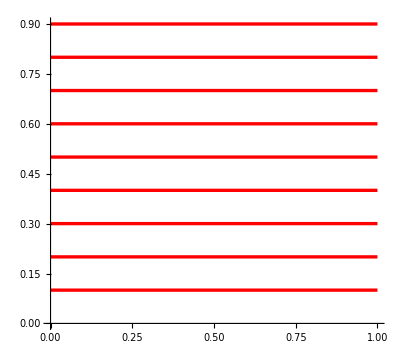

```mathematica
Table[{θ1,C1},{C1,1/10,9/10,1/10}];
Curve1=ParametricPlot[{%},{θ1,0,1},PlotStyle->Directive[Thickness[.006],Red]]
```

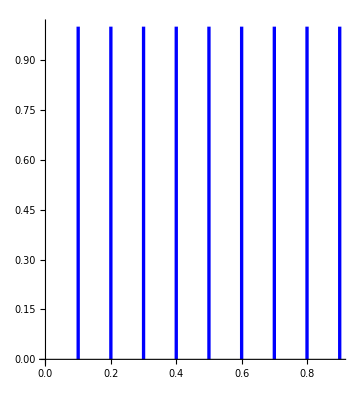

```mathematica
Table[{C2,θ2},{C2,1/10,9/10,1/10}];
Curve2=ParametricPlot[{%},{θ2,0,1},PlotStyle->Directive[Thickness[.006],Blue]]
```

```mathematica
Ref1=ParametricPlot[{X,Y},{X,0,1},{Y,0,1},PlotStyle->Directive[RGBColor[0.618,0.618,0.618]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Axes->False,Frame->False,PerformanceGoal->"Quality"];
```

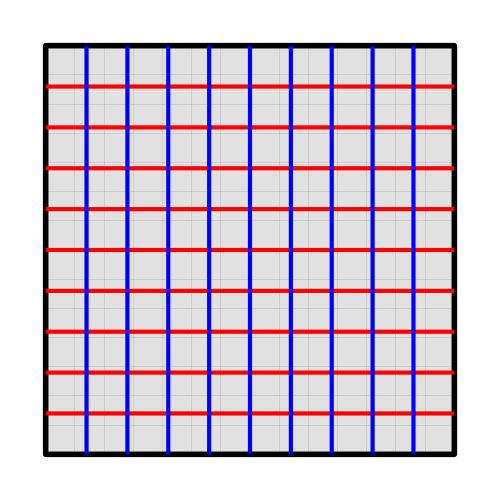

```mathematica
Show[Ref1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

```mathematica
-(z)^3-z^3 I/.{z-> X+I*Y}
ComplexExpand[%]
```

(-1-ⅈ) (X+ⅈ Y)^3

-X^3+3 X^2 Y+3 X Y^2-Y^3+ⅈ (-X^3-3 X^2 Y+3 X Y^2+Y^3)

```mathematica
{x0[X_,Y_],y0[X_,Y_]}={-X^3+3 X^2 Y+3 X Y^2-Y^3,(-X^3-3 X^2 Y+3 X Y^2+Y^3)}
```

{-X^3+3 X^2 Y+3 X Y^2-Y^3,-X^3-3 X^2 Y+3 X Y^2+Y^3}

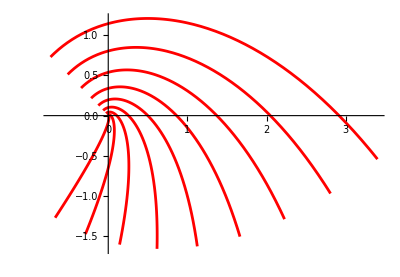

```mathematica
Curve1=ParametricPlot[Table[{x0[X,Y0],y0[X,Y0]},{Y0,1/10,9/10,1/10}],{X,0,1},PlotStyle->Directive[Thickness[.005],Red],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

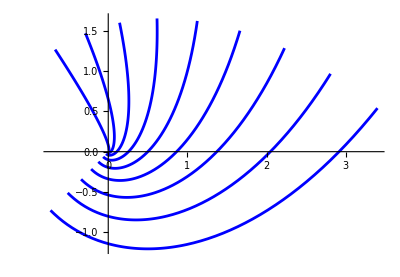

```mathematica
Curve2=ParametricPlot[Table[{x0[X0,Y],y0[X0,Y]},{X0,1/10,9/10,1/10}],{Y,0,1},PlotStyle->Directive[Thickness[.005],Blue],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

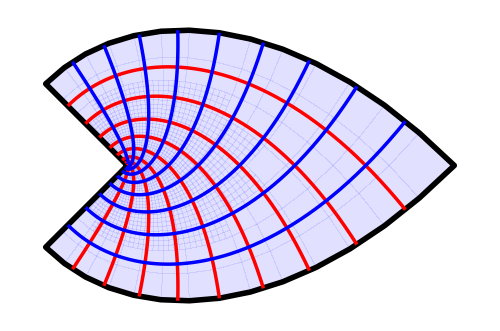

```mathematica
Cur1=ParametricPlot[{x0[X,Y],y0[X,Y]},{X,0,1},{Y,0,1},PlotStyle->Directive[RGBColor[0.618,0.618,1]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Frame->False,Axes->False,PerformanceGoal->"Quality"];
Show[Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

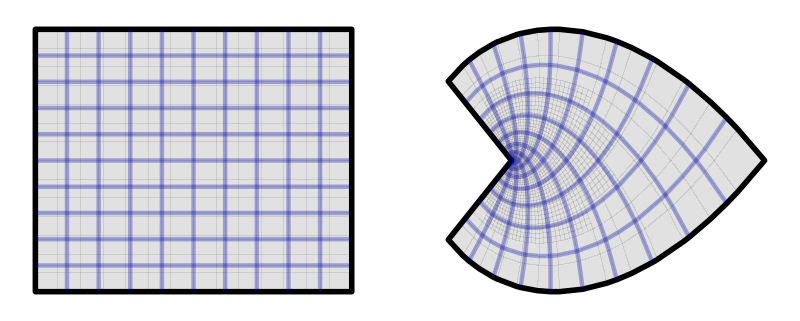

```mathematica
{fig1,fig2}=With[{z=x+I*y},ParametricPlot[ReIm[#],{x,0,1},{y,0,1},Mesh->9,MaxRecursion->2,PlotStyle->RGBColor[0.618,0.618,0.618],MeshStyle->Directive[Thickness[.008],Darker[Blue]],BoundaryStyle->Directive[Thickness[.010],Black],Frame->False,Axes->False]]&/@{z,-(z)^3-z^3 I};
GraphicsRow[{fig1,fig2}]
```

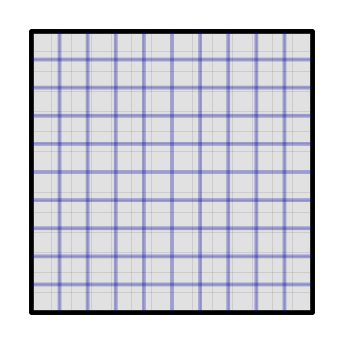

```mathematica
fig1
```

f(z)=z^2

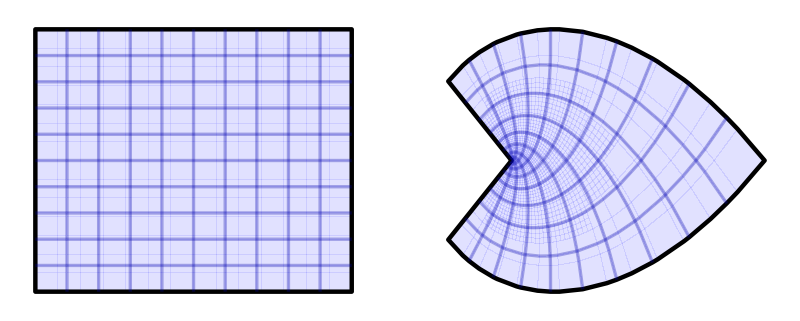

```mathematica
{fig1,fig2}=With[{z=x+I*y},ParametricPlot[ReIm[#],{x,0,1},{y,0,1},Mesh->9,MaxRecursion->2,PlotStyle->RGBColor[0.618,0.618,1],MeshStyle->Directive[Thickness[.006],Darker[Blue]],BoundaryStyle->Directive[Thickness[.008],Black],Frame->False,Axes->False]]&/@{z,-(z)^3-z^3 I};
GraphicsRow[{fig1,fig2}]
```

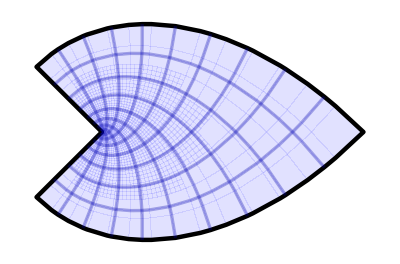

```mathematica
fig2
```